# Periods, Life and Death Expectancies

## Periods

```mathematica
BasinPeriodMu0000000000001=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Period\\outputCycPeriod_mu = 1e-12.dat","Table"];BasinPeriodMu00000000001=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Period\\outputCycPeriod_mu = 1e-10.dat","Table"];
BasinPeriodMu000000001=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Period\\outputCycPeriod_mu = 1e-08.dat","Table"];
BasinPeriodMu0000001=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Period\\outputCycPeriod_mu = 1e-06.dat","Table"];
BasinPeriodMu000001=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Period\\outputCycPeriod_mu = 1e-05.dat","Table"];
BasinPeriodMu000002=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Period\\outputCycPeriod_mu = 2e-05.dat","Table"];
BasinPeriodMu000003=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Period\\outputCycPeriod_mu = 3e-05.dat","Table"];
```

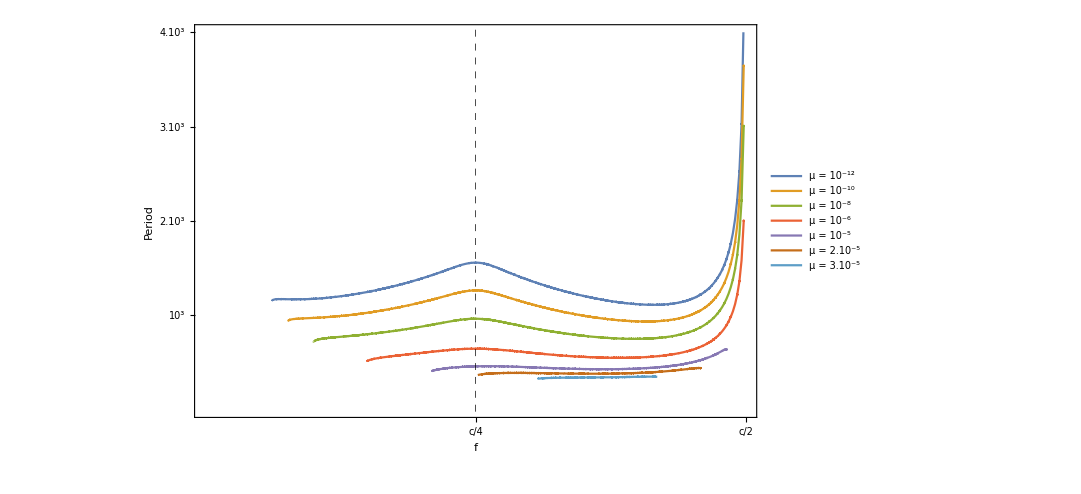

```mathematica
FigPer=ListLinePlot[{BasinPeriodMu0000000000001,BasinPeriodMu00000000001,BasinPeriodMu000000001,BasinPeriodMu0000001,BasinPeriodMu000001,BasinPeriodMu000002,BasinPeriodMu000003},PlotStyle->Thick,PlotLegends->{"μ = 10^-12","μ = 10^-10","μ = 10^-8","μ = 10^-6","μ = 10^-5","μ = 2.10^-5","μ = 3.10^-5"},PlotRange->{{0,0.25},{0,4000}},Frame->True,FrameTicks->{{{{1000,"10^3"},{2000,"2.10^3"},{3000,"3.10^3"},{4000,"4.10^3"}},None},{{{0.125,"c/4"},{0.25,"c/2"}},None}},FrameStyle->Directive[Black,Thick],FrameLabel->{Style["f",22,Italic],Style["Period",22,Italic]},FrameTicksStyle->Directive[Black,Bold,16,Opacity[1],FontOpacity->1],FrameStyle->Directive[Bold,Black,18],GridLines->{{0.125},None},GridLinesStyle->Directive[Black,Dashed],ImageSize->{800,600}]
```

```mathematica
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Mutation Model\\Basin_of_attraction\\AttractionBasinWithMutMAC\\Period.eps",FigPer];
```

## Life Expectancies

```mathematica
BasinLifeAndDeathMu0000000000001=Import["/Users/fred/Dropbox/Fyon/RecombinationHotspost/Mutation Model/Basin_of_attraction/AttractionBasinWithMutMAC/outputCycLifeAndDeath_mu = 1e-12.dat","Table"];
BasinLifeAndDeathMu00000000001=Import["/Users/fred/Dropbox/Fyon/RecombinationHotspost/Mutation Model/Basin_of_attraction/AttractionBasinWithMutMAC/outputCycLifeAndDeath_mu = 1e-10.dat","Table"];
BasinLifeAndDeathMu000000001=Import["/Users/fred/Dropbox/Fyon/RecombinationHotspost/Mutation Model/Basin_of_attraction/AttractionBasinWithMutMAC/outputCycLifeAndDeath_mu = 1e-08.dat","Table"];
BasinLifeAndDeathMu0000001=Import["/Users/fred/Dropbox/Fyon/RecombinationHotspost/Mutation Model/Basin_of_attraction/AttractionBasinWithMutMAC/outputCycLifeAndDeath_mu = 1e-06.dat","Table"];
BasinLifeAndDeathMu000001=Import["/Users/fred/Dropbox/Fyon/RecombinationHotspost/Mutation Model/Basin_of_attraction/AttractionBasinWithMutMAC/outputCycLifeAndDeath_mu = 1e-05.dat","Table"];
BasinLifeAndDeathMu000002=Import["/Users/fred/Dropbox/Fyon/RecombinationHotspost/Mutation Model/Basin_of_attraction/AttractionBasinWithMutMAC/outputCycLifeAndDeath_mu = 2e-05.dat","Table"];
```

```mathematica
LEMu0000000000001=BasinLifeAndDeathMu0000000000001[[;;,1;;2]];
LEMu00000000001=BasinLifeAndDeathMu00000000001[[;;,1;;2]];
LEMu000000001=BasinLifeAndDeathMu000000001[[;;,1;;2]];
LEMu0000001=BasinLifeAndDeathMu0000001[[;;,1;;2]];
```

```mathematica
DEMu0000000000001=BasinLifeAndDeathMu0000000000001[[;;,{1,3}]];
DEMu00000000001=BasinLifeAndDeathMu00000000001[[;;,{1,3}]];
DEMu000000001=BasinLifeAndDeathMu000000001[[;;,{1,3}]];
DEMu0000001=BasinLifeAndDeathMu0000001[[;;,{1,3}]];
```

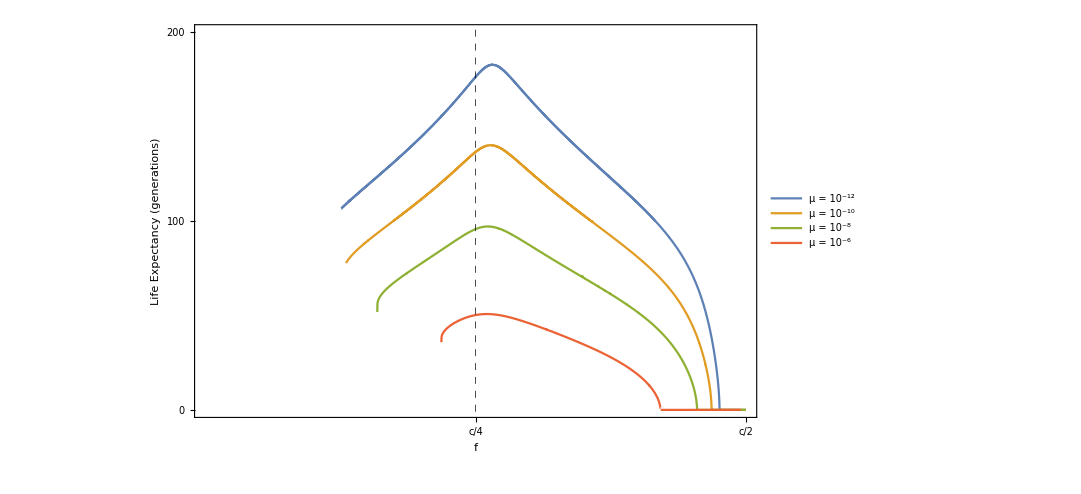

```mathematica
FigLE=ListLinePlot[{LEMu0000000000001,LEMu00000000001,LEMu000000001,LEMu0000001},PlotStyle->Thick,PlotLegends->{"μ = 10^-12","μ = 10^-10","μ = 10^-8","μ = 10^-6"},PlotRange->{{0,0.5},{0,200}},Frame->True,FrameTicks->{{{{0,"0"},{100,"100"},{200,"200"}},None},{{{0.25,"c/4"},{0.5,"c/2"}},None}},FrameStyle->Directive[Black,Thick],FrameLabel->{Style["f",22,Italic],Style["Life Expectancy (generations)",22,Italic]},FrameTicksStyle->Directive[Black,Bold,16,Opacity[1],FontOpacity->1],FrameStyle->Directive[Bold,Black,18],GridLines->{{0.25},None},GridLinesStyle->Directive[Black,Dashed],ImageSize->{800,600}]
```

```mathematica
Export["/Users/fred/Dropbox/Fyon/RecombinationHotspost/Mutation Model/Basin_of_attraction/AttractionBasinWithMutMAC/LifeExpectancy.jpg",FigLE];
```

## Death Expectancies

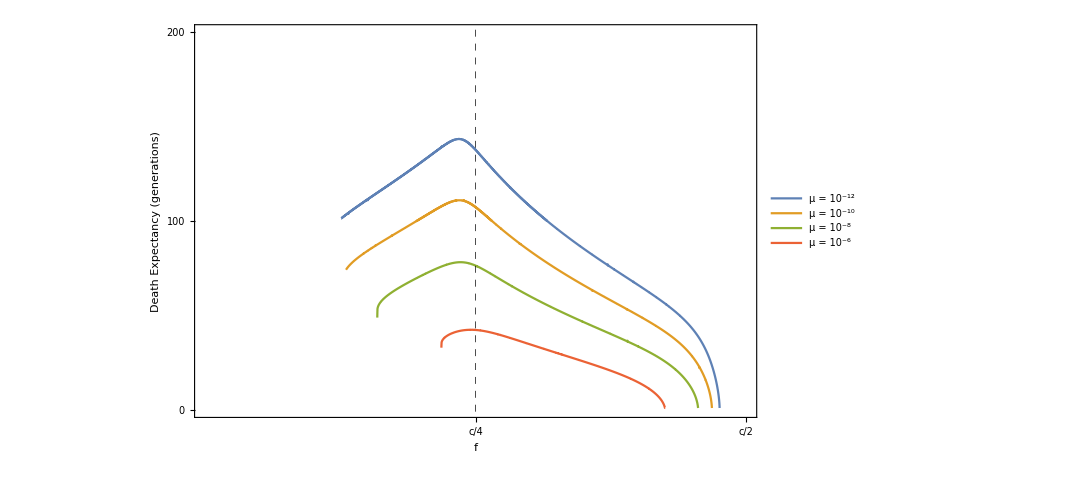

```mathematica
FigDE=ListLinePlot[{DEMu0000000000001,DEMu00000000001,DEMu000000001,DEMu0000001},PlotStyle->Thick,PlotLegends->{"μ = 10^-12","μ = 10^-10","μ = 10^-8","μ = 10^-6"},PlotRange->{{0,0.5},{0,200}},Frame->True,FrameTicks->{{{{0,"0"},{100,"100"},{200,"200"}},None},{{{0.25,"c/4"},{0.5,"c/2"}},None}},FrameStyle->Directive[Black,Thick],FrameLabel->{Style["f",22,Italic],Style["Death Expectancy (generations)",22,Italic]},FrameTicksStyle->Directive[Black,Bold,16,Opacity[1],FontOpacity->1],FrameStyle->Directive[Bold,Black,18],GridLines->{{0.25},None},GridLinesStyle->Directive[Black,Dashed],ImageSize->{800,600}]
```

```mathematica
Export["/Users/fred/Dropbox/Fyon/RecombinationHotspost/Mutation Model/Basin_of_attraction/AttractionBasinWithMutMAC/DeathExpectancy.jpg",FigDE];
```